```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2+c03 x^3+c04 x^4, 0≤x≤1}, {c11(x-1)+c12(x-1)^2+c13(x-1)^3+c14(x-1)^4, 1<x≤2}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
```

1+c01+c02+c03+c04

c11+c12+c13+c14

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[f[x+1]+f[x]+f[x-1]+f[x-2],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[-f[x+1]+f[x-1]+2f[x-2],x>0&&x<1],x]
```

{2+c01+c02+c03+c04+c11+c12+c13+c14,-2 c02-3 c03-4 c04-2 c12-3 c13-4 c14,2 c02+3 c03+4 c04+2 c12+3 c13+4 c14+2 (c04+c14),-4 (c04+c14),2 (c04+c14)}

{1+c01+c02+c03+c04+2 c11+2 c12+2 c13+2 c14,-c01-2 c02-3 c03-4 c04-3 c11-4 c12-6 c13-8 c14,c02+3 c03+6 c04+c12+6 c13+12 c14,-c03-4 c04-3 c13-8 c14,c04+c14}

```mathematica
(*Smoothness*)
Df=Simplify[D[f[x],x],x>0]/.Abs'[x]->1
c01+x (2 c02+x (3 c03+4 c04 x))/.x->1
c11+(2 c12+(3 c13+4 c14 (-1+x)) (-1+x)) (-1+x)/.x->1
c11+(2 c12+(3 c13+4 c14 (-1+x)) (-1+x)) (-1+x)/.x->2
```

Piecewise[{{c01+x (2 c02+x (3 c03+4 c04 x)), x≤1}, {c11+(2 c12+(3 c13+4 c14 (-1+x)) (-1+x)) (-1+x), 1<x≤2}, {0, True}}]

c01+2 c02+3 c03+4 c04

c11

c11+2 c12+3 c13+4 c14

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0,
	c01==0,
	c01+2 c02+3 c03+4 c04==c11,
	c11+2 c12+3 c13+4 c14==0
	},
	{c01,c02,c03,c04,c11,c12,c13,c14}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c01→0,c03→-7/2-2 c02,c04→5/2+c02,c11→-1/2,c12→-3/2-c02,c13→9/2+2 c02,c14→-5/2-c02}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-3)^5 ∑_(j=-3)^5 W1[i-j]f[x-i,y-j]/.GenSol;
{SumF1a1,SumF1a2,SumF1a3,SumF1a4}=Parallelize[{
	Simplify[SumF1,x>0&&x<1&&y>0&&y<1],
	Simplify[SumF1,x>0&&x<1&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>2&&y<3]}];
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4}=Parallelize[{
	FullSimplify[D[SumF1a1,{{x,y}}]],
	FullSimplify[D[SumF1a2,{{x,y}}]],
	FullSimplify[D[SumF1a3,{{x,y}}]],
	FullSimplify[D[SumF1a4,{{x,y}}]]}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4}=Parallelize[{
	Simplify[SumF1,x>1&&x<2&&y>0&&y<1],
	Simplify[SumF1,x>1&&x<2&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-2&&y<-1]}];
{DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4}=Parallelize[{
	FullSimplify[D[SumF1b1,{{x,y}}]],
	FullSimplify[D[SumF1b2,{{x,y}}]],
	FullSimplify[D[SumF1b3,{{x,y}}]],
	FullSimplify[D[SumF1b4,{{x,y}}]]}];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4}=Parallelize[{
	Simplify[∫_0^1 ∫_0^1 (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_0^1 (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_-1^0 (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-1^0 (DSumF1a4.{1,1})^2 ⅆxⅆy]}];
```

```mathematica
{Err1b1,Err1b2,Err1b3,Err1b4}=Parallelize[{
	Simplify[∫_0^1 ∫_1^2 (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_1^2 (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_2^3 (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_2^3 (DSumF1b4.{1,1})^2 ⅆxⅆy]}];
```

```mathematica
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1b1+Err1b2+Err1b3+Err1b4];
```

```mathematica
Err=FullSimplify[Err1 /.φ->1/2]
DErr=FullSimplify[D[Err,{{c02}}]];
H=FullSimplify[D[Err,{{c02},2}]];
Sols=RootReduce[Solve[DErr==0,c02]];
N[Sols]
Sols[[3]]
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

(9318135+8 c02 (993711+2 c02 (190117+56 c02 (361+14 c02))))/33868800

{{c02→-8.79369+3.62046 ⅈ},{c02→-8.79369-3.62046 ⅈ},{c02→-1.7519}}

{c02→Root[993711+760468 #1+121296 #1^2+6272 #1^3&,1]}

1 | 0.813096-0.330049 ⅈ | False
2 | 0.813096+0.330049 ⅈ | False
3 | 0.0917079 | True

{c01→0.,c03→0.00379778,c04→0.748101,c11→-0.5,c12→0.251899,c13→0.996202,c14→-0.748101,c02→-1.7519}

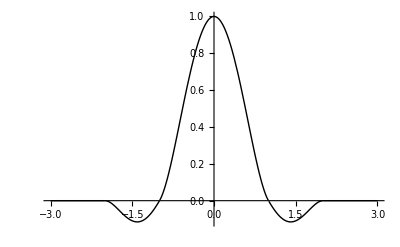

```mathematica
Sol=Sols[[3]];
FullSol=N[Join[GenSol/.Sol,Sol]]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```